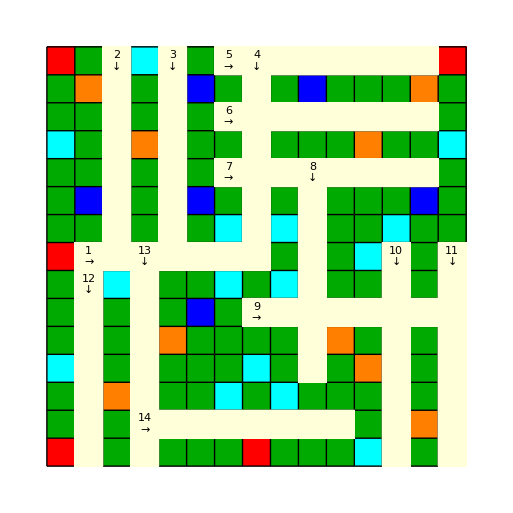
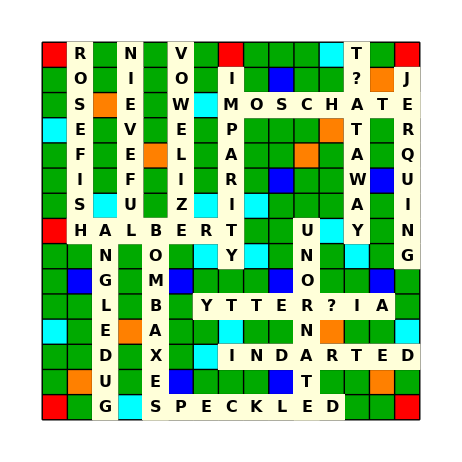
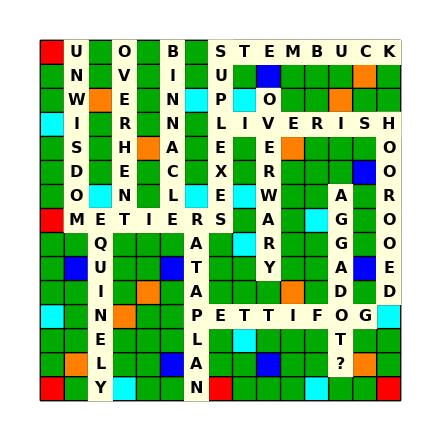

```mathematica
CanFormWord[tiles_,word_]:=AllTrue[
  Tally[Characters[word]],
  (Count[Characters[tiles],#[[1]]]>=#[[2]])&
]

Select[wordsByLength[8],CanFormWord["AAAAEFFGGIIIIJOOQVVXY",#]&]
```

{}

```mathematica
possibleWords={};
Do[
  Do[
    AppendTo[possibleWords,Select[wordsByLength[8],CanFormWord[StringJoin["AAAAAADEEFFGJY",s1,s2],#]&]],
    {s1,ToUpperCase[Alphabet[]]}
  ],
  {s2,ToUpperCase[Alphabet[]]}
];
```

```mathematica
Sort[DeleteDuplicates[Flatten[possibleWords]]]
```

{ADJUTAGE,AFFEARED,AFFEARES,AFFECTED,AFFEERED,AFFLATED,AFFRAYED,AFFRAYER,AGRAFFES,AMENAGED,AMYGDALA,AMYGDALE,APANAGED,AVERAGED,BALAYAGE,BAYADEER,BAYADERE,DEEJAYED,DEFANGED,DEFRAYAL,DEFRAYED,DEFRAYER,DELEGACY,DRAYAGES,EDGEWAYS,EFFRAIDE,EFFULGED,ENDAMAGE,FADEAWAY,FALDAGES,FANEGADA,FANFARED,FARADAYS,FARDAGES,FEDAYEEN,FEDERACY,FEDERARY,FEEDBAGS,FEEDYARD,FEIJOADA,FENAGLED,FRAPEAGE,FROGEYED,GADARENE,GALEATED,GANYMEDE,GEARHEAD,GOFFERED,GRAYHEAD,GREYHEAD,GUFFAWED,GYNAECEA,HEADAGES,HEADGATE,HEADGEAR,JAGGEDER,JAGGEDLY,JANNEYED,LAAGERED,LAYERAGE,LEAFAGES,MEGADEAL,MEGADYNE,METAYAGE,PAJAMAED,PAYGRADE,PYJAMAED,REAEDIFY,REDAMAGE,STAFFAGE,WAYFARED,YARDAGES}

Tiles Used: 84 AAAAAAAABBCCDDDDEEEEEEEEEFFGGGHHIIIIIIIIIKLLLLMMNNNNNNOOOOOOOOPPRRRRRRSSSSTTTTUUVWYZ

Tiles Left: 16 AEEEJQTTUUVWXY??

### Visualize

```mathematica
assoc=<|1-><|"Bingo"->"BRASHED","Position"->{"H",2},"Direction"->"Right"|>,2-><|"Bingo"->"SPATTERS","Position"->{"A",5},"Direction"->"Down","Overlap"->"S"|>,3-><|"Bingo"->"AMOEBOID","Position"->{"H",4},"Direction"->"Down","Overlap"->"A"|>,4-><|"Bingo"->"UNCLOSED","Position"->{"A",8},"Direction"->"Down","Overlap"->"D"|>,5-><|"Bingo"->"DOWNCOME","Position"->{"O",4},"Direction"->"Right","Overlap"->"D"|>,6-><|"Bingo"->"EUTAXITE","Position"->{"G",8},"Direction"->"Right","Overlap"->"E"|>,7-><|"Bingo"->"ZOOPHORI","Position"->{"E",7},"Direction"->"Right","Overlap"->"O"|>,8-><|"Bingo"->"CRUSTILY","Position"->{"C",8},"Direction"->"Right","Overlap"->"C"|>,9-><|"Bingo"->"DEVELING","Position"->{"F",15},"Direction"->"Down","Overlap"->"E"|>,10-><|"Bingo"->"TINKERER","Position"->{"A",3},"Direction"->"Down","Overlap"->"R"|>,11-><|"Bingo"->"UNWIVING","Position"->{"A",8},"Direction"->"Right","Overlap"->"U"|>,12-><|"Bingo"->"OBLIQUER","Position"->{"L",3},"Direction"->"Right","Overlap"->"B"|>|>
```

<|1→<|Bingo→BRASHED,Position→{H,2},Direction→Right|>,2→<|Bingo→SPATTERS,Position→{A,5},Direction→Down,Overlap→S|>,3→<|Bingo→AMOEBOID,Position→{H,4},Direction→Down,Overlap→A|>,4→<|Bingo→UNCLOSED,Position→{A,8},Direction→Down,Overlap→D|>,5→<|Bingo→DOWNCOME,Position→{O,4},Direction→Right,Overlap→D|>,6→<|Bingo→EUTAXITE,Position→{G,8},Direction→Right,Overlap→E|>,7→<|Bingo→ZOOPHORI,Position→{E,7},Direction→Right,Overlap→O|>,8→<|Bingo→CRUSTILY,Position→{C,8},Direction→Right,Overlap→C|>,9→<|Bingo→DEVELING,Position→{F,15},Direction→Down,Overlap→E|>,10→<|Bingo→TINKERER,Position→{A,3},Direction→Down,Overlap→R|>,11→<|Bingo→UNWIVING,Position→{A,8},Direction→Right,Overlap→U|>,12→<|Bingo→OBLIQUER,Position→{L,3},Direction→Right,Overlap→B|>|>

```mathematica
epilogState={};

Do[
word=assoc[[i]]["Bingo"];
pos=assoc[[i]]["Position"];
dir=assoc[[i]]["Direction"];
epilogState=UpdateScrabbleBoard[word,pos,dir,epilogState];,
{i,Length[assoc]}
]
```

```mathematica
Iconize@epilogState
```